```mathematica
(*b=Subscript[Δ, 1]/Δ*)
```

```mathematica
b=0.2;
```

```mathematica
(*β=u/c*)
```

```mathematica
beta=0.8;
```

```mathematica
(*Domain*)
```

```mathematica
xmin=-100.0;
xmax=100.0;
tmin=0.0;
tmax=1.0;
```

```mathematica
(*Kink*)
```

```mathematica
F[alpha_]:=NIntegrate[1/Sqrt[Sqrt[1+b^2*(1-Cos[x])]-1],{x,Pi,alpha},MaxRecursion->1000]
```

```mathematica
list=Table[{F[alpha]/2,alpha},{alpha,10^-5,2*Pi,0.0005}];//Timing
```

{59.998,Null}

```mathematica
fun=Interpolation[list,InterpolationOrder->1]
```

InterpolatingFunction[{{-64.5454,50.2255}},<>]

```mathematica
maxKsi=Max[list[[All,1]]];
minKsi=Min[list[[All,1]]];
kink[x_]:=Piecewise[{{fun[x],x≤ maxKsi&&x≥ minKsi},{N[2*Pi],x≥maxKsi},{0.0,x≤minKsi}}]
listk=Table[{x,kink[x]},{x,xmin,xmax,0.1}];
k=Interpolation[listk,InterpolationOrder->1]
```

InterpolatingFunction[{{-100.,100.}},<>]

```mathematica
stmp=OpenWrite["kink.dat"]
```

OutputStream[kink.dat,30]

```mathematica
Write[stmp,Length[listk]];For[i=1,i≤ Length[listk],i++,Write[stmp,listk[[i]][[1]]];Write[stmp,listk[[i]][[2]]];]
```

```mathematica
Close[stmp]
```

kink.dat

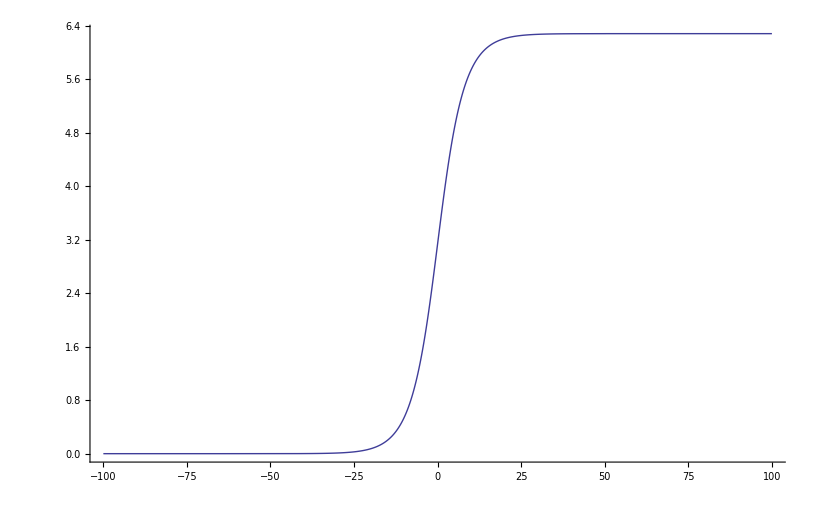

```mathematica
ListPlot[listk,Joined->True]
```

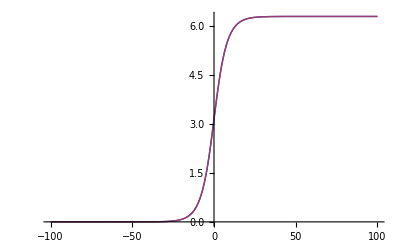

```mathematica
Plot[{k[x],kink[x]},{x,xmin,xmax}]
```

```mathematica
(*Single-soliton*)
```

```mathematica
solution=f/.First[NDSolve[{D[f[t,x], t,t]==D[f[t,x], x,x]-b^2*Sin[f[t,x]]/Sqrt[1+b^2*(1-Cos[f[t,x]])],f[tmin,x]==k[(x-beta*tmin)/Sqrt[1-beta^2]],Derivative[1,0][f][tmin,x]==k'[(x-beta*tmin)/Sqrt[1-beta^2]],f[t,xmin]==0,f[t,xmax]==2*Pi},f,{t,tmin,tmax},{x,xmin,xmax},MaxSteps->{1000,100000}]]
```

InterpolatingFunction::dmval: Input value {-166.667} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-159.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-152.778} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::mxsst: Using maximum number of grid points 100000 allowed by the MaxPoints or MinStepSize options for independent variable x.

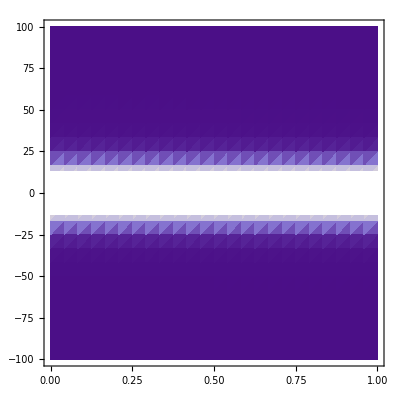

```mathematica
DensityPlot[Derivative[1,0][solution][t,x],{t,tmin,tmax},{x,xmin,xmax}, PlotPoints->25,Mesh->False]
```

```mathematica
F[alpha_,b_]:=2*Sqrt[1+b^2*(1-Cos[alpha])]
```

```mathematica
Manipulate[
ContourPlot[beta^2/2+2*Sqrt[1+b^2*(1-Cos[alpha])],{alpha,-5,5},{beta,-5,5}],
{b,0.001,10}
]
```

```mathematica
<<EquationTrekker`
```

```mathematica
b=10;EquationTrekker[y''[t]+b^2*Sin[y[t]]/Sqrt[1+b^2*(1-Cos[y[t]])]==0,y,{t,0,100}]
```

```mathematica
Series[2*Sqrt[1+b^2*(1-Cos[alpha])],{b,0,3}]
```

2+(1-Cos[alpha]) b^2+O[b]^4

```mathematica
F[3,1,2]
```

0.113327

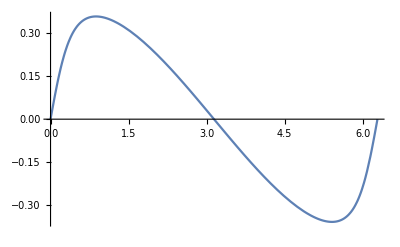

```mathematica
Plot[F[x,10],{x,0,2*Pi}]
```

```mathematica
SeriesCoefficient[1/Sqrt[1+x],{x,0,n}]
```

Piecewise[{{Binomial[-1/2,n], n≥0}, {0, True}}]

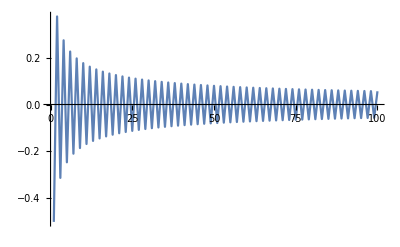

```mathematica
ListLinePlot[Table[Binomial[-1/2,n],{n,1,100}]]
```

```mathematica
DSolve[{y''[x]+2 y'[x]+y[x]==2+x,y[0]==1,y'[0]==2},y[x],x]
```

{{y[x]→ⅇ^-x (1+2 x+ⅇ^x x)}}

```mathematica
Simplify[9*(x+3)^2-(x-4)^2+9*(y-5)^2-(y-2)^2]
```

286+62 x+8 x^2-86 y+8 y^2



```mathematica
a=Graph[{1<->2,2<->3,3<->1}]
```

```mathematica
Needs["Combinatorica`"]
```

```mathematica
ChromaticNumber[a]
```

ChromaticNumber[-Graphics-]

```mathematica
GraphData[a,"ChromaticNumber"]
```

GraphData::notdef: GraphData has no value associated with the specified argument(s).

GraphData[-Graphics-,ChromaticNumber]

```mathematica
PropertyList[a]
```

{GraphHighlight,GraphHighlightStyle,GraphLayout,GraphStyle,EdgeShapeFunction,EdgeStyle,VertexCoordinates,VertexShapeFunction,VertexShape,VertexSize,VertexStyle}

```mathematica
ChromaticNumber[a]
```

ChromaticNumber[-Graphics-]

```mathematica
\
```